## Kinetic energies of electron in 2 Pi a0 box

```mathematica
hbar=6.58212 10^-16; (* eV s *)
```

```mathematica
me=5.68563 10^-12; (* eV s^2/m^2 *)
```

```mathematica
a0=0.529 10^-10 ;(* m *)
```

```mathematica
En[qn_]:=(qn  Pi  hbar/(2 Pi a0))^2/(2 me);  (* eV *)
```

```mathematica
Lambda[qn_]:=1/qn; (* 2 Pi a0 *)
```

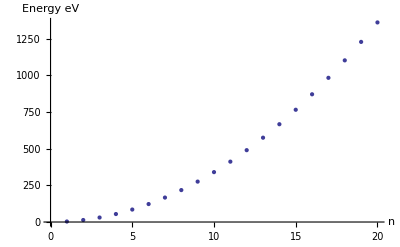

```mathematica
ListPlot[Table[En[qn],{qn,20}],{AxesLabel->{n,Energy (eV)}}]
```

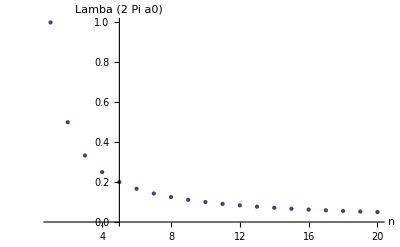

```mathematica
ListPlot[Table[Lambda[qn],{qn,20}],AxesLabel->{n,"Lamba (2 Pi a0)"},PlotRange->Full]
```

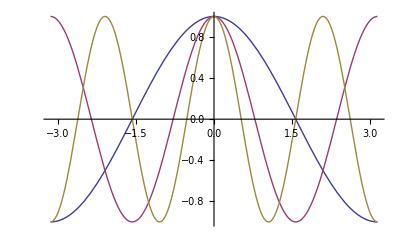

```mathematica
Plot[{Cos[x/Lambda[1]],Cos[x/Lambda[2]],Cos[x/Lambda[3]]},{x,-Pi,Pi}]
```

## Z=10 (Ne) hydrogenic orbitals

```mathematica
Z=10;
```

```mathematica
Clear[Z]
```

## One s orbital

```mathematica
OneS=Piecewise[{{Exp[-Z r],r≥0},{Exp[Z r],r<0}}];
```

```mathematica
OneSNorm=Integrate[OneS*OneS,{r,-Infinity,Infinity},Assumptions->Z > 0];
```

```mathematica
OneS=OneS/Sqrt[OneSNorm];
```

```mathematica
Z=10;
```

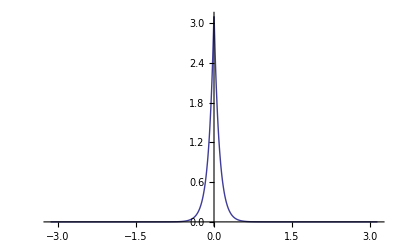

```mathematica
Plot[OneS,{r,-Pi,Pi},PlotRange->Full]
```

## Fourier cosine series expansions

Expand function f(|r|) in domain -Pi, Pi in series of cosines

n = 1

```mathematica
OneTerm=FourierCosSeries[OneS,r,1]
```

-(-1+ⅇ^(-10 π))/(√10 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[r])/(101 π)

n = 1 - 2

```mathematica
Two=FourierCosSeries[OneS,r,2]
```

-(-1+ⅇ^(-10 π))/(√10 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[r])/(101 π)+(√(5/2) (5-5 ⅇ^(-10 π)) Cos[2 r])/(13 π)

n = 1 - 3

```mathematica
Three=FourierCosSeries[OneS,r,3]
```

-(-1+ⅇ^(-10 π))/(√10 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[r])/(101 π)+(√(5/2) (5-5 ⅇ^(-10 π)) Cos[2 r])/(13 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[3 r])/(109 π)

n = 1 - 10

```mathematica
Ten=FourierCosSeries[OneS,r,10]
```

-(-1+ⅇ^(-10 π))/(√10 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[r])/(101 π)+(√(5/2) (5-5 ⅇ^(-10 π)) Cos[2 r])/(13 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[3 r])/(109 π)+(√10 (5-5 ⅇ^(-10 π)) Cos[4 r])/(29 π)+(√(2/5) (4+4 ⅇ^(-10 π)) Cos[5 r])/(5 π)+(√(5/2) (5-5 ⅇ^(-10 π)) Cos[6 r])/(17 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[7 r])/(149 π)+(√10 (5-5 ⅇ^(-10 π)) Cos[8 r])/(41 π)+(20 √10 (1+ⅇ^(-10 π)) Cos[9 r])/(181 π)-((-1+ⅇ^(-10 π)) Cos[10 r])/(√10 π)

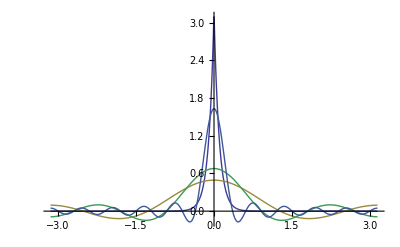

```mathematica
Plot[{OneS,One, Two, Three,Ten},{r,-Pi,Pi},PlotRange->Full]
```

## Two s orbital

```mathematica
Clear[Z];
```

```mathematica
TwoS=Piecewise[{{(1-Z r ) Exp[-Z r/2],r≥0},{(1+Z r)Exp[Z r/2],r<0}}];
```

```mathematica
TwoSNorm=Integrate[TwoS*TwoS,{r,-Infinity,Infinity},Assumptions->Z>0]
```

2/Z

```mathematica
TwoS=TwoS/Sqrt[TwoSNorm];
```

```mathematica
Z=10;
```

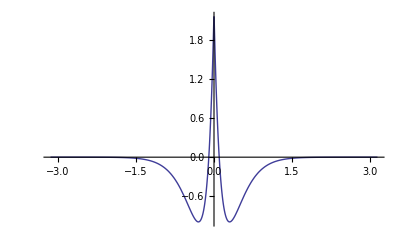

```mathematica
Plot[TwoS,{r,-Pi,Pi},PlotRange->Full]
```

```mathematica
OneTerm2s = FourierCosSeries[TwoS,r,1]
```

(ⅇ^(-5 π) (2-2 ⅇ^(5 π)+20 π))/(2 √5 π)-(5 √5 ⅇ^(-5 π) (11+11 ⅇ^(5 π)+130 π) Cos[r])/(169 π)

```mathematica
TwoTerm2s = FourierCosSeries[TwoS,r,2]
```

(ⅇ^(-5 π) (2-2 ⅇ^(5 π)+20 π))/(2 √5 π)-(5 √5 ⅇ^(-5 π) (11+11 ⅇ^(5 π)+130 π) Cos[r])/(169 π)-(10 √5 ⅇ^(-5 π) (-13+13 ⅇ^(5 π)-290 π) Cos[2 r])/(841 π)

```mathematica
FiveTerm2s=FourierCosSeries[TwoS,r,5]
```

(ⅇ^(-5 π) (2-2 ⅇ^(5 π)+20 π))/(2 √5 π)-(5 √5 ⅇ^(-5 π) (11+11 ⅇ^(5 π)+130 π) Cos[r])/(169 π)-(10 √5 ⅇ^(-5 π) (-13+13 ⅇ^(5 π)-290 π) Cos[2 r])/(841 π)+(5 √5 ⅇ^(-5 π) (1+ⅇ^(5 π)-170 π) Cos[3 r])/(289 π)+(10 √5 ⅇ^(-5 π) (-23+23 ⅇ^(5 π)+410 π) Cos[4 r])/(1681 π)+(ⅇ^(-5 π) (1+ⅇ^(5 π)-10 π) Cos[5 r])/(√5 π)

```mathematica
TenTerm2s=FourierCosSeries[TwoS,r,10]
```

(ⅇ^(-5 π) (2-2 ⅇ^(5 π)+20 π))/(2 √5 π)-(5 √5 ⅇ^(-5 π) (11+11 ⅇ^(5 π)+130 π) Cos[r])/(169 π)-(10 √5 ⅇ^(-5 π) (-13+13 ⅇ^(5 π)-290 π) Cos[2 r])/(841 π)+(5 √5 ⅇ^(-5 π) (1+ⅇ^(5 π)-170 π) Cos[3 r])/(289 π)+(10 √5 ⅇ^(-5 π) (-23+23 ⅇ^(5 π)+410 π) Cos[4 r])/(1681 π)+(ⅇ^(-5 π) (1+ⅇ^(5 π)-10 π) Cos[5 r])/(√5 π)+(10 √5 ⅇ^(-5 π) (-83+83 ⅇ^(5 π)+610 π) Cos[6 r])/(3721 π)+(5 √5 ⅇ^(-5 π) (61+61 ⅇ^(5 π)-370 π) Cos[7 r])/(1369 π)+(10 √5 ⅇ^(-5 π) (-167+167 ⅇ^(5 π)+890 π) Cos[8 r])/(7921 π)+(5 √5 ⅇ^(-5 π) (109+109 ⅇ^(5 π)-530 π) Cos[9 r])/(2809 π)+(2 ⅇ^(-5 π) (-11+11 ⅇ^(5 π)+50 π) Cos[10 r])/(25 √5 π)

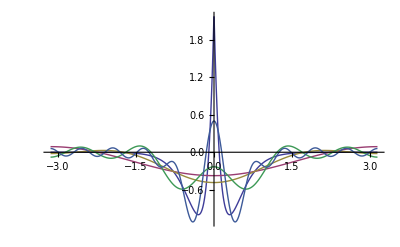

```mathematica
Plot[{TwoS,OneTerm2s,TwoTerm2s,FiveTerm2s,TenTerm2s},{r,-Pi,Pi},PlotRange->All]
```

## OPW idea

```mathematica
Overlap=Integrate[OneS*TwoS,{r,-Infinity,Infinity}]
```

(2 √2)/9

```mathematica
N[2/45 ⅇ^(-15 π) (-1+ⅇ^(15 π)+30 π),5]
```

0.044444

```mathematica
Overlap=1
```

1

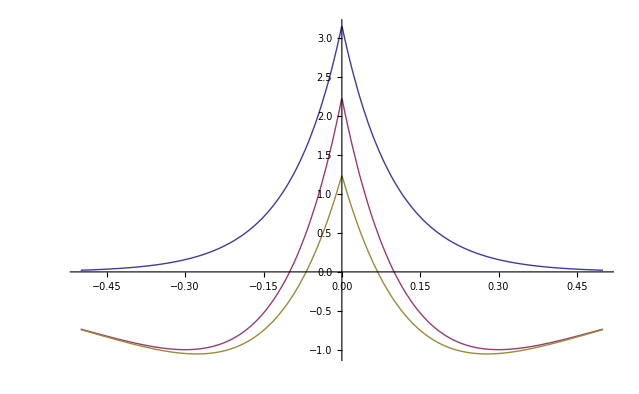

```mathematica
Plot[{OneS, TwoS,TwoS-Overlap OneS},{r,-0.5,0.5},PlotRange->Full]
```

```mathematica
Show[%156,ImageSize->Full]
```

Show::gtype: Out is not a type of graphics.

Show[%156,ImageSize→Full]